## Galerkin Method FEM for Linear PB eqn

### Obtaining Eqns

0. d^2 ψ(x)/dx^2 = -f(x)
1. Discretize domain into elements
2. Develope (simpler) equations to approximate 
    the solution of each element.
3. Example (2 grid points):
	ψ̃ = N_1(x)ψ_1+N_2(x)ψ_2
	d^2 ψ(x)/dx^2+f(x) = 0
d^2 ψ̃(x)/dx^2+f(x) = err(x)
(∂∫_D (err(x))^2 dD)/(∂α_i) = 0 = ∫_D err(x)N_i(x)dD, where N_i(x)=∂/(∂α_ii)err(x)
∫_D [d^2 ψ̃(x)/dx^2+f(x)] N(x) dD = ∫_D err(x) N(x)dD
	
-Graphics-
(∫_x_1^x_2 (d ψ̃)/dx dN_1/(∂x)ⅆx   
∫_x_1^x_2 (d ψ̃)/dx dN_2/dx ⅆx  ) =  (-(dψ̃(x_1))/dx  
-(dψ̃(x_2))/dx) +  (∫_x_1^x_2 f(x)N_1(x)ⅆx  
∫_x_1^x_2 f(x)N_2(x)ⅆx )
1/(x_2-x_1)(1  | -1
-1  | 1) ((ψ̃)_1
(ψ̃)_2) =  (-(d ψ̃ (x_1))/dx  
-(dψ̃(x_2))/dx)+  (∫_x_1^x_2 f(x)N_1(x)ⅆx  
∫_x_1^x_2 f(x)N_2(x)ⅆx )  
      Element Stiffness       Boundary Conditions        External effects

(∂^2 ψ(z))/(∂z^2) = κ^2 sinh[ψ(z)]
 (∂^2 ψ(z))/(∂z^2) = κ^2 ψ(z)
ψ(z) = ψ0 exp(-κ z)

T(z) = ∑_(i=1)^M N_i(z)ψ_i
(∂^2 T(z))/(∂z^2)- κ^2 T(z) = err(z)

Least squared FEM (Galerkin Method)
∂/(∂α_i)(∑_(j=1)^M err_j^2) = 0
∂/(∂α_i)(∫_D (err(x))^2 ⅆD) = 0
∫_D err(x)W_i ⅆD=0

Let W_i = N_i(z)
∫_D err(x)W_i ⅆD= ∫_z_1^z_M [(∂^2 T(z))/(∂z^2)- κ^2 T(z) ]N_i(z)ⅆz = 0

basis function N_i(z):
-Graphics-

∫_z_1^z_M [(∂^2 T(z))/(∂z^2)]N_i(z)ⅆz = ∫_z_1^z_M [ κ^2 T(z) ]N_i(z)ⅆz 
(∂T(z))/(∂z) N_i(z)|_z_1^z_M - ∫_z_1^z_M (∂T(z))/(∂z)(∂N_i(z))/(∂z)ⅆz  (LHS: integration by parts)
Look at the first term
i=1, N_1(z)(∂T)/(∂z)|_z_1^z_M= N_1(z_M)(∂T)/(∂z) - N_1(z_1)(∂T)/(∂z) = -(∂T)/(∂z)|_z_1
i=2, N_2(z)(∂T)/(∂z)|_z_1^z_M= N_2(z_M)(∂T)/(∂z) - N_2(z_1)(∂T)/(∂z) = 0
i=M, N_M(z)(∂T)/(∂z)|_z_1^z_M= N_M(z_M)(∂T)/(∂z) - N_M(z_1)(∂T)/(∂z) = (∂T)/(∂z)|_z_M
(∫_z_1^z_M (∂T(z))/(∂z)(∂N_1(z))/(∂z)ⅆz + ∫_z_1^z_M [ κ^2 T(z) ]N_1(z)ⅆz  
∫_z_1^z_M (∂T(z))/(∂z)(∂N_2(z))/(∂z)ⅆz  + ∫_z_1^z_M [ κ^2 T(z) ]N_2(z)ⅆz
:
:
∫_z_1^z_M (∂T(z))/(∂z)(∂N_M(z))/(∂z)ⅆz  + ∫_z_1^z_M [ κ^2 T(z) ]N_M(z)ⅆz)=(-(∂T)/(∂z)(z_1) 
0
:
:
(∂T)/(∂z)(z_M)  )

i=1, ∫_z_1^z_M (∂T(z))/(∂z)(∂N_1(z))/(∂z)ⅆz  = ∫_z_1^z_2 (∂T(z))/(∂z) (-1/Δz)ⅆz = 1/Δz (ψ_1-ψ_2)
i=2, ∫_z_1^z_M (∂T(z))/(∂z)(∂N_2(z))/(∂z)ⅆz  = ∫_z_1^z_2 (∂T(z))/(∂z) (1/Δz)ⅆz+∫_z_2^z_3 (∂T(z))/(∂z) (-1/Δz)ⅆz = 1/Δz (T_2-T_1)+1/Δz(T_2-T_3) = 1/Δz (2 ψ_2-ψ_1-ψ_3)
i=3, ∫_z_1^z_M (∂T(z))/(∂z)(∂N_3(z))/(∂z)ⅆz  = ∫_z_2^z_3 (∂T(z))/(∂z) (1/Δz)ⅆz+∫_z_3^z_4 (∂T(z))/(∂z) (-1/Δz)ⅆz = 1/Δz (T_3-T_2)+1/Δz(T_3-T_4) = 1/Δz (2 ψ_3-ψ_2-ψ_4)
i=M, ∫_z_1^z_M (∂T(z))/(∂z)(∂N_M(z))/(∂z)ⅆz  = ∫_(z_(M-1))^z_M (∂T(z))/(∂z) (1/Δz)ⅆz = 1/Δz (ψ_M-ψ_(M-1))
(∫_z_1^z_M (∂T(z))/(∂z)(∂N_1(z))/(∂z)ⅆz  
∫_z_1^z_M (∂T(z))/(∂z)(∂N_2(z))/(∂z)ⅆz  
:
:
∫_z_1^z_M (∂T(z))/(∂z)(∂N_M(z))/(∂z)ⅆz  ) = 1/Δz (ψ_1-ψ_2  
2 ψ_2-ψ_1-ψ_3 
:
:
ψ_M-ψ_(M-1)  ) = 1/Δz(1 | -1 | ... | ... | ... | 0
-1 | 2 | -1 | ... | ... | 0
0 | -1 | 2 | -1 | ... | 0
: | : | : | : | : | :
0 | ... | ... | 0 | -1 | 1)(ψ_1  
ψ_2 
:
:
ψ_M )

i=1, ∫_z_1^z_M [ κ^2 T(z) ]N_1(z)ⅆz  = κ^2∫_z_1^z_2 [ κ^2 T(z) ]N_1(z)ⅆz = κ^2∫_z_1^z_2 [ψ_1 (1-1/Δz (z-z_1))+ψ_2 (1/Δz (z-z_1))](1-1/Δz (z-z_1))ⅆz = κ^2(Δz/3 ψ_1+ Δz/6 ψ_2)
i=2, ∫_z_1^z_M [ κ^2 T(z) ]N_2(z)ⅆz  = κ^2∫_z_1^z_3 [ κ^2 T(z) ]N_2(z)ⅆz 
= κ^2∫_z_1^z_2 [ψ_1 (1-1/Δz (z-z_1))+ψ_2 (1/Δz (z-z_1))](1/Δz (z-z_1))ⅆz  + κ^2∫_z_2^z_3 [ψ_2 (1-1/Δz (z-z_2))+ψ_3 (1/Δz (z-z_2))](1-1/Δz (z-z_2))ⅆz
=  κ^2 (Δz/6 ψ_1+(Δz 2)/3 ψ_2+Δz/6 ψ_3)
i=M, ∫_z_1^z_M [ κ^2 T(z) ]N_M(z)ⅆz =∫_(z_(M-1))^z_M [ κ^2 T(z) ]N_M(z)ⅆz = = κ^2(Δz/3 ψ_M+ Δz/6 ψ_(M-1))
(∫_z_1^z_M [ κ^2 T(z) ]N_1(z)ⅆz  
∫_z_1^z_M [ κ^2 T(z) ]N_2(z)ⅆz
:
:
∫_z_1^z_M [ κ^2 T(z) ]N_M(z)ⅆz  )= κ^2 Δz (ψ_1/3+ψ_2/6  
ψ_1/6+(2 ψ_2)/3+ψ_3/6 
:
:
(ψ_(M-1))/6+ψ_M/3  )=κ^2 Δz(1/3 | 1/6 | ... | ... | ... | 0
1/6 | 2/3 | 1/6 | ... | ... | 0
0 | 1/6 | 2/3 | 1/6 | ... | 0
: | : | : | : | : | :
0 | ... | ... | 0 | 1/6 | 1/2)(ψ_1  
ψ_2 
:
:
ψ_M )

1/Δz(1 | -1 | ... | ... | ... | 0
-1 | 2 | -1 | ... | ... | 0
0 | -1 | 2 | -1 | ... | 0
: | : | : | : | : | :
0 | ... | ... | 0 | -1 | 1)(ψ_1  
ψ_2 
:
:
ψ_M ) +κ^2 Δz(1/3 | 1/6 | ... | ... | ... | 0
1/6 | 2/3 | 1/6 | ... | ... | 0
0 | 1/6 | 2/3 | 1/6 | ... | 0
: | : | : | : | : | :
0 | ... | ... | 0 | 1/6 | 1/3)(ψ_1  
ψ_2 
:
:
ψ_M ) = (-(∂ψ)/(∂z)(z_1) 
0
:
:
(∂ψ)/(∂z)(z_M)  )
A X + B sinh(X) = C
A X + corr*B X = -B [sinh(X) - corr*X] + C

### FEM solutions for linear PB (The program starts from here, must run before the nolinear PB)

1/Δz(1 | -1 | ... | ... | ... | 0
-1 | 2 | -1 | ... | ... | 0
0 | -1 | 2 | -1 | ... | 0
: | : | : | : | : | :
0 | ... | ... | 0 | -1 | 1)(ψ_1  
ψ_2 
:
:
ψ_M ) +κ^2 Δz(1/3 | 1/6 | ... | ... | ... | 0
1/6 | 2/3 | 1/6 | ... | ... | 0
0 | 1/6 | 2/3 | 1/6 | ... | 0
: | : | : | : | : | :
0 | ... | ... | 0 | 1/6 | 1/3)(sinhψ_1  
sinhψ_2 
:
:
sinhψ_M ) = (-(∂ψ)/(∂z)(z_1) 
0
:
:
(∂ψ)/(∂z)(z_M)  )

```mathematica
ψ[ψ0_,κ_,z_]:=ψ0 Exp[-κ z]
```

```mathematica
ngrid={5,10,20,30,40,60};(* numbers of grids in z axis *)
L=3; (* range of domain *)
dL=Table[L/ngrid[[i]],{i,1,Length[ngrid]}]; (* grid spacing *)
kappa=2; (* for PB *)
ψ0=-6; (* for PB*)
```

```mathematica
MatrixA=Table[Table[Table[0,{i,1,ngrid[[k]]}],{j,1,ngrid[[k]]}],{k,1,Length[ngrid]}];
Do[
Do[
Which[j==1 ,MatrixA[[k]][[j,1]]=1;MatrixA[[k]][[j,2]]=-1,
j==ngrid[[k]],MatrixA[[k]][[j,ngrid[[k]]-1]]=-1;MatrixA[[k]][[j,ngrid[[k]]]]=1,
1<j<ngrid[[k]],MatrixA[[k]][[j,j-1]]=-1;MatrixA[[k]][[j,j]]=2;MatrixA[[k]][[j,j+1]]=-1
];
,{j,1,ngrid[[k]]}]
MatrixA[[k]]=1/dL[[k]] MatrixA[[k]];
,{k,1,Length[ngrid]}]
```

```mathematica
MatrixB=Table[Table[Table[0,{i,1,ngrid[[k]]}],{j,1,ngrid[[k]]}],{k,1,Length[ngrid]}];
Do[
Do[
Which[j==1 ,MatrixB[[k]][[j,1]]=1/3;MatrixB[[k]][[j,2]]=1/6,
j==ngrid[[k]],MatrixB[[k]][[j,ngrid[[k]]-1]]=1/6;MatrixB[[k]][[j,ngrid[[k]]]]=1/3,
1<j<ngrid[[k]],MatrixB[[k]][[j,j-1]]=1/6;MatrixB[[k]][[j,j]]=2/3;MatrixB[[k]][[j,j+1]]=1/6
];
,{j,1,ngrid[[k]]}]
MatrixB[[k]]=kappa^2 dL[[k]] MatrixB[[k]];
,{k,1,Length[ngrid]}]
```

```mathematica
Vec=Table[0,{i,1,Length[ngrid]}];
Do[
Vec[[k]]=Table[0,{i,1,ngrid[[k]]}];
Vec[[k]][[1]]=-D[ψ[ψ0,kappa,z],z]/.z->0;
Vec[[k]][[ngrid[[k]]]]=D[ψ[ψ0,kappa,z],z]/.z->dL[[k]]*(ngrid[[k]]-1);
,{k,1,Length[ngrid]}]
```

```mathematica
FEMsol=Table[0,{i,1,Length[ngrid]}];
Do[
FEMsol[[k]]=LinearSolve[MatrixA[[k]]+MatrixB[[k]],Vec[[k]]];
,{k,1,Length[ngrid]}]
```

```mathematica
Pana=Show[Plot[ψ[ψ0,kappa,z],{z,0,L},PlotRange->All,PlotStyle->Red,PlotLabel->Style["d^2/dz^2 = κ^2ψ",FontSize->16],PlotLegends->Placed[{Style["ψ(z)=ψ_0exp(-κz)",FontSize->16]},{0.5,0.5}]],PlotRange->{All,{ψ0,0}},Frame->True,FrameStyle->Thick,FrameLabel->{"z (λ_D)","ψ"},LabelStyle->Black,BaseStyle->{FontWeight->"Bold",FontSize->16},AxesStyle->{Black,Black},ImageSize->Medium];
```

```mathematica
Plist=Table[ListPlot[Table[{dL[[k]] (i-1),FEMsol[[k]][[i]]},{i,1,ngrid[[k]]}],PlotMarkers->Style["◆", 10,Blue],PlotLegends->Placed[{Style[Row[{"FEM ngrid = ",ngrid[[k]]}],FontSize->16]},{0.46,0.3}],Joined->True,PlotStyle->Gray,PlotRange->All]
,{k,1,Length[ngrid]}];
```

```mathematica
Manipulate[Show[Pana,Plist[[n]]],{n,1,Length[ngrid],1,Appearance->"Open"}]
```

### FEM solutions for nonlinear PB (use initial guess from the linear PB)

```mathematica
ψNL[ψ0_,κ_,z_]:=4 ArcTanh[Exp[-κ z] Tanh[ψ0/4]]
```

```mathematica
VecNL=Table[0,{i,1,Length[ngrid]}];
Do[
VecNL[[k]]=Table[0,{i,1,ngrid[[k]]}];
VecNL[[k]][[1]]=-D[ψNL[ψ0,kappa,z],z]/.z->0;
VecNL[[k]][[ngrid[[k]]]]=D[ψNL[ψ0,kappa,z],z]/.z->dL[[k]]*(ngrid[[k]]-1);
,{k,1,Length[ngrid]}]
```

```mathematica
oldsol=Table[0,{i,1,Length[ngrid]}];
newsol=Table[0,{i,1,Length[ngrid]}];
Do[
stop=False;
imax=150;
tol=10^-4;
corr=40;(*to prevent getting too small numbers than computer limit*)
oldsol[[k]]=N[FEMsol[[k]]];
Do[
fsol=Sinh[oldsol[[k]]]-oldsol[[k]]*corr;
Bfsol=MatrixB[[k]].fsol;
newsol[[k]]=LinearSolve[MatrixA[[k]]+corr*MatrixB[[k]],-Bfsol+VecNL[[k]]];
Do[If[Abs[newsol[[k]][[j]]-oldsol[[k]][[j]]]>10^-4,oldsol[[k]]=newsol[[k]];Break[],stop=True],{j,1,Length[newsol[[k]]]}];
If[stop==True,Print["Numerical solutions converged at ",i,"th iteration"];Break[],If[i==imax,Print["Failed to converge in ",imax," iterations.\n Errors: ",Table[Abs[newsol[[k]][[j]]-oldsol[[k]][[j]]],{j,1,Length[newsol[[k]]]}]]]]
,{i,1,imax}]
,{k,1,Length[ngrid]}]
```

Numerical solutions converged at 62th iteration

Numerical solutions converged at 67th iteration

Numerical solutions converged at 68th iteration

Numerical solutions converged at 102th iteration

Numerical solutions converged at 80th iteration

Numerical solutions converged at 50th iteration

```mathematica
PanaNL=Show[Plot[ψNL[ψ0,kappa,z],{z,0,L},PlotRange->All,PlotStyle->Red,PlotLabel->Style["d^2/dz^2 = κ^2sinh(ψ)",FontSize->16],PlotLegends->Placed[{Style["ψ(z)=4Tanh^-1(e^-κzTanh(ψ0/4))",FontSize->16]},{0.55,0.37}]],PlotRange->{All,{ψ0,1.5}},Frame->True,FrameStyle->Thick,FrameLabel->{"z (λ_D)","ψ"},LabelStyle->Black,BaseStyle->{FontWeight->"Bold",FontSize->16},AxesStyle->{Black,Black},ImageSize->Medium];
```

```mathematica
PNLlist=Table[ListPlot[Table[{dL[[k]] (i-1),newsol[[k]][[i]]},{i,1,ngrid[[k]]}],PlotMarkers->Style["◆", 10,Blue],PlotLegends->Placed[{Style[Row[{"FEM ngrid = ",ngrid[[k]]}],FontSize->16]},{0.4,0.23}],Joined->True,PlotStyle->Gray,PlotRange->All]
,{k,1,Length[ngrid]}];
```

```mathematica
Manipulate[Show[PanaNL,PNLlist[[n]]],{n,1,Length[ngrid],1,Appearance->"Open"}]
```

### Performance on linear and nonliner PB

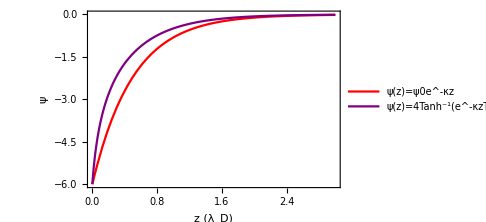

```mathematica
Show[Plot[ψ[ψ0,kappa,z],{z,0,L},PlotRange->All,PlotStyle->Red,PlotLegends->{Style["ψ(z)=ψ0e^-κz",FontSize->16]}],Plot[ψNL[ψ0,kappa,z],{z,0,L},PlotRange->All,PlotStyle->Purple,PlotLegends->{Style["ψ(z)=4Tanh^-1(e^-κzTanh(ψ0/4))",FontSize->16]}],PlotRange->{All,{ψ0,0}},Frame->True,FrameStyle->Thick,FrameLabel->{"z (λ_D)","ψ"},LabelStyle->Black,BaseStyle->{FontWeight->"Bold",FontSize->16},AxesStyle->{Black,Black},ImageSize->Medium]
```

```mathematica
Manipulate[Grid[{{Show[Pana,Plist[[n]]],Show[PanaNL,PNLlist[[n]]]}}],{n,1,Length[ngrid],1,Appearance->"Open"}]
```

```mathematica
SetDirectory["~/Desktop"]
```

/Volumes/750G_Home/Users/appleowner/Desktop

```mathematica
Do[
Export[FileNameJoin[{Directory[],"t1.pdf"}],Grid[{{Show[Pana,Plist[[n]]],Show[PanaNL,PNLlist[[n]]]}}]]
,{n,1,1}]
```

```mathematica
Manipulate[First@Import[FileNameJoin[{Directory[],"p"<>ToString[n]<>".pdf"}]],{n,1,6,1}]
```

```mathematica
NotebookLocate["t1"]
CDFDeploy["~/Desktop/test.cdf",NotebookSelection[],Method->"Standalone"];
```

## Finite difference method

Kapper and Honig, PROTEINS: Structurem Function, and Genetics, 1, 47-59, 1986

E(r) = -∇ϕ(r)
D(r) = ϵ(r)E(r) = -ϵ(r)∇ϕ(r)

∇·D(r) = q(r)
∇·ϵ(r)∇ϕ(r) + q = 0
q=q_fixed+q_free

q_free can be modeled by a Boltzmann distribution, giving:
q_free = -2 Zeρ^0 sinh(βeZϕ(r)) = -(κ̄)^2sinh[ψ(z)] 
         =  -(κ̄)^2ψ(z)[1+(ψ(z))^2/6+(ψ(r))^4/120+ ...]	
, where (κ̄)^2 = ϵ_r κ^2 = (2 Z^2 e^2 ρ^0)/(ϵ_0 k_B T)

∇·ϵ_r(r)∇ϕ(r)-(κ̄)^2 ϕ(r) + (q_fixed(r))/ϵ_0 = 0

∫∫∫∇·ϵ_r(r)∇ϕ(r)  d^3 r = ∫∫∫(κ̄)^2 ϕ(r)  d^3 r -∫∫∫(q_fixed(r))/ϵ_0 d^3 r  

∮ϵ_r(r)∇ϕ(r)  dA=(κ̄)^2 ϕ_0 h^3 + Q_0/ϵ_0 

∑ϵ_i(ϕ_i-ϕ_0)h =(κ̄)^2 ϕ_0 h^3 + Q_0/ϵ_0  

ϕ_0 = (∑ϵ_i ϕ_i + Q_0/ϵ_0)/(∑ϵ_i + (κ̄)^2 h^2)